## Исходные данные

### Рандомные

```mathematica
data1 = Import["C:\\Users\\griho\\OneDrive\\Рабочий стол\\Параллели\\N_body_cuda\\traj___1.txt","Table"];
data2 = Import["C:\\Users\\griho\\OneDrive\\Рабочий стол\\Параллели\\N_body_cuda\\traj___2.txt","Table"];
data3 = Import["C:\\Users\\griho\\OneDrive\\Рабочий стол\\Параллели\\N_body_cuda\\traj___3.txt","Table"];
data4 = Import["C:\\Users\\griho\\OneDrive\\Рабочий стол\\Параллели\\N_body_cuda\\traj___4.txt","Table"];
data5 = Import["C:\\Users\\griho\\OneDrive\\Рабочий стол\\Параллели\\N_body_cuda\\traj1.txt","Table"];
data6 = Import["C:\\Users\\griho\\OneDrive\\Рабочий стол\\Параллели\\N_body_cuda\\traj2.txt","Table"];
data7 = Import["C:\\Users\\griho\\OneDrive\\Рабочий стол\\Параллели\\N_body_cuda\\traj3.txt","Table"];
data8 = Import["C:\\Users\\griho\\OneDrive\\Рабочий стол\\Параллели\\N_body_cuda\\traj4.txt","Table"];
l1=ListPointPlot3D[data1,PlotStyle->Hue[0.1]];
l2=ListPointPlot3D[data2,PlotStyle->Hue[0.3]];
l3=ListPointPlot3D[data3,PlotStyle->Hue[0.5]];
l4=ListPointPlot3D[data4,PlotStyle->Hue[0.7]];
Show[l1,l2,l3,l4,PlotRange->Full]
```

-Graphics3D-

```mathematica
l5=ListPointPlot3D[data5,PlotStyle->Hue[0.1]];
l6=ListPointPlot3D[data6,PlotStyle->Hue[0.3]];
l7=ListPointPlot3D[data7,PlotStyle->Hue[0.5]];
l8=ListPointPlot3D[data8,PlotStyle->Hue[0.7]];
Show[l5,l6,l7,l8,PlotRange->Full]
```

-Graphics3D-

### Точное решение

```mathematica
data1n201 = Import["C:\\Users\\griho\\OneDrive\\Рабочий стол\\Параллели\\N_body_cuda\\Точность\\traj1_201.txt","Table"];
data1n401 = Import["C:\\Users\\griho\\OneDrive\\Рабочий стол\\Параллели\\N_body_cuda\\Точность\\traj1_401.txt","Table"];
data1n801 = Import["C:\\Users\\griho\\OneDrive\\Рабочий стол\\Параллели\\N_body_cuda\\Точность\\traj1_801.txt","Table"];
data1n1601 = Import["C:\\Users\\griho\\OneDrive\\Рабочий стол\\Параллели\\N_body_cuda\\Точность\\traj1_1601.txt","Table"];
data1n3201 = Import["C:\\Users\\griho\\OneDrive\\Рабочий стол\\Параллели\\N_body_cuda\\Точность\\traj1_3201.txt","Table"];
data1Exact = Import["C:\\Users\\griho\\OneDrive\\Рабочий стол\\Параллели\\N_body_cuda\\Точность\\traj1.txt","Table"];
data2Exact = Import["C:\\Users\\griho\\OneDrive\\Рабочий стол\\Параллели\\N_body_cuda\\Точность\\traj2.txt","Table"];
data3Exact = Import["C:\\Users\\griho\\OneDrive\\Рабочий стол\\Параллели\\N_body_cuda\\Точность\\traj3.txt","Table"];
data4Exact = Import["C:\\Users\\griho\\OneDrive\\Рабочий стол\\Параллели\\N_body_cuda\\Точность\\traj4.txt","Table"];
dataEx1=Table[Delete[data1Exact[[i]],1],{i,1,Length[data1Exact]}];
dataEx2=Table[Delete[data2Exact[[i]],1],{i,1,Length[data2Exact]}];
dataEx3=Table[Delete[data3Exact[[i]],1],{i,1,Length[data3Exact]}];
dataEx4=Table[Delete[data4Exact[[i]],1],{i,1,Length[data4Exact]}];
```

```mathematica
lEx1=ListPointPlot3D[dataEx1,PlotStyle->Hue[0.2]];
lEx2=ListPointPlot3D[dataEx2,PlotStyle->Hue[0.4]];
lEx3=ListPointPlot3D[dataEx3,PlotStyle->Hue[0.6]];
lEx4=ListPointPlot3D[dataEx4,PlotStyle->Hue[0.8]];
l1=ListPointPlot3D[data1,PlotStyle->Hue[0.2]];
l2=ListPointPlot3D[data2,PlotStyle->Hue[0.4]];
l3=ListPointPlot3D[data3,PlotStyle->Hue[0.6]];
l4=ListPointPlot3D[data4,PlotStyle->Hue[0.8]];
Show[lEx1,lEx2,lEx3,lEx4,PlotRange->Full]
```

-Graphics3D-

```mathematica
Show[l1,l2,l3,l4,PlotRange->Full]
```

-Graphics3D-

## Порядок

```mathematica
Error201 = Table[√((data1n201[[i]][[1]]-dataEx1[[i]][[1]])^2+(data1n201[[i]][[2]]-dataEx1[[i]][[2]])^2+(data1n201[[i]][[3]]-dataEx1[[i]][[3]])^2),{i,1,Length[dataEx1]}];
Error401=Table[√((data1n401[[(i-1)*2+1]][[1]]-dataEx1[[i]][[1]])^2+(data1n401[[(i-1)*2+1]][[2]]-dataEx1[[i]][[2]])^2+(data1n401[[(i-1)*2+1]][[3]]-dataEx1[[i]][[3]])^2),{i,1,Length[dataEx1]}];
Error801=Table[√((data1n801[[(i-1)*4+1]][[1]]-dataEx1[[i]][[1]])^2+(data1n801[[(i-1)*4+1]][[2]]-dataEx1[[i]][[2]])^2+(data1n801[[(i-1)*4+1]][[3]]-dataEx1[[i]][[3]])^2),{i,1,Length[dataEx1]}];
Error1601=Table[√((data1n1601[[(i-1)*8+1]][[1]]-dataEx1[[i]][[1]])^2+(data1n1601[[(i-1)*8+1]][[2]]-dataEx1[[i]][[2]])^2+(data1n1601[[(i-1)*8+1]][[3]]-dataEx1[[i]][[3]])^2),{i,1,Length[dataEx1]}];
Error3201=Table[√((data1n3201[[(i-1)*16+1]][[1]]-dataEx1[[i]][[1]])^2+(data1n3201[[(i-1)*16+1]][[2]]-dataEx1[[i]][[2]])^2+(data1n3201[[(i-1)*16+1]][[3]]-dataEx1[[i]][[3]])^2),{i,1,Length[dataEx1]}];
Total[Error201]
Total[Error401]
Total[Error801]
Total[Error1601]
Total[Error3201]
```

2.01126

0.530124

0.135993

0.0343299

0.00851513

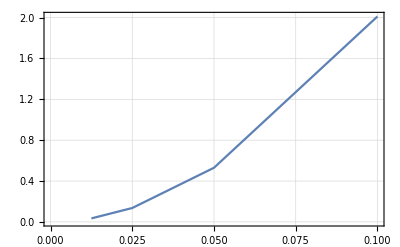

```mathematica
ListLinePlot[{{0.1,Total[Error201]},{0.05,Total[Error401]},{0.025,Total[Error801]},{0.0125,Total[Error1601]}},PlotTheme->"Detailed"]
```

```mathematica
Grid[{{tau,0.1,0.05,0.025,0.0125,0.00625},{p^n,,Total[Error201]/Total[Error401],Total[Error401]/Total[Error801],Total[Error801]/Total[Error1601],Total[Error1601]/Total[Error3201]}},Frame->All]
```

tau | 0.1 | 0.05 | 0.025 | 0.0125 | 0.00625
p^n |  | 3.79394 | 3.89816 | 3.96136 | 4.03164

## Время

### N = 10, M = 50 000

```mathematica
Grid[{{block_size,t_double,t_float,New,t_double,t_float},{64,0.054176,0.027411,,0.055414,0.031868},{128,0.048639,0.025355,,0.050555,0.026927},{256,0.057668,0.029040,,0.059470,0.031419},{512,0.073495,0.034154,,0.077760,0.039574}},Frame->All]
```

block_size | t_double | t_float | New | t_double | t_float
64 | 0.054176 | 0.027411 |  | 0.055414 | 0.031868
128 | 0.048639 | 0.025355 |  | 0.050555 | 0.026927
256 | 0.057668 | 0.02904 |  | 0.05947 | 0.031419
512 | 0.073495 | 0.034154 |  | 0.07776 | 0.039574

### N = 10, M = 200 000

```mathematica
Grid[{{block_size,t_double,t_float},{64,0.756581,0.397294},{128,736787,0.390676},{256,0.734491,0.390451},{512,0.876003,0.387000}},Frame->All]
```

block_size | t_double | t_float
64 | 0.756581 | 0.397294
128 | 736787 | 0.390676
256 | 0.734491 | 0.390451
512 | 0.876003 | 0.387

### N = 10, M = 500 000

```mathematica
Grid[{{block_size,t_double,t_float},{64,4.660731,2.170289},{128,4.633050,2.259826},{256,4.573356,2.231489},{512,5.113457,2.235242}},Frame->All]
```

block_size | t_double | t_float
64 | 4.66073 | 2.17029
128 | 4.63305 | 2.25983
256 | 4.57336 | 2.23149
512 | 5.11346 | 2.23524

### Сравнить времена при 18 потоках, M = 50 000, N = 10.

```mathematica
Grid[{{MPI,CUDA128,CUDA64,CUDA128NEW,CUDA64NEW},{3.71624,0.049631,0.056278,0.050511,0.055764}},Frame->All]
```

MPI | CUDA128 | CUDA64 | CUDA128NEW | CUDA64NEW
3.71624 | 0.049631 | 0.056278 | 0.050511 | 0.055764

```mathematica
3.71624/0.049631
```

74.8774